# 关于素数的一些探讨

```mathematica
Table[Prime[i (2)+j+3],{i,0,n},{j,0,n}]
```

```mathematica
({{5, 7}, {11, 13}})
Det[%]
```

-12

```mathematica
n=1;a=Table[Abs[Det[Table[Prime[i (n+1)+j+l],{i,0,n},{j,0,n}]]],{l,3,20000}];Min[a]
```

12

```mathematica
ListPlot[a]
```

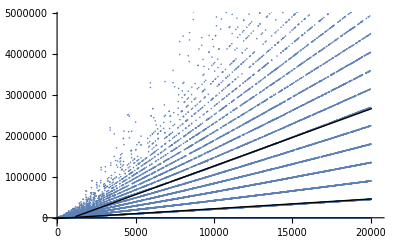

```mathematica
b=Table[Abs[Det[Table[Prime[i (n+1)+j+l],{i,0,n},{j,0,n}]]],{l,20000,50000}];
```

```mathematica
Min[b]
```

12

我们发现如果把相邻四个素数构成的矩阵的行列式记做：D_i=|P_i*P_(i+3)-P_(i+1)*P_(i+2)|
有如上图所示的很好的分布，除去这一分布的特殊性，我们还可以观察到其中的绝对值最小值除了前两个值1和2以外，之后最小的就只有12了
所以我们就猜想当i>2时，我们总是有Di>=12


首先可以分析出12具体代表什么

```mathematica
Simplify[x(x+8)-(x+6)(x+2)]
```

-12

换言之，他们是两组相邻的孪生素数
所谓相邻就是说他们是（p，p+2）以及（p+6，p+8）
一个比较初等的观察是(p,p+2,p+4)不能同时为素数，
原因是必有3的倍数在其中，
由此也可以粗略看出i比较大时，
Di不能比12小了

接下来对Di进行估计

```mathematica
Expand[x(x+m)-(x+l)(x+k)]
```

-k l-k x-l x+m x

```mathematica
x(m-l-k)-kl
```

x<x+l<x+k<x+m 为相邻4个素数，当x充分大的时候，我们总是有x>>kl
结合l，k均为偶数以及（0，l，k）模3不能互不同余，所以kl>=12

### 关于D_i图像特殊性的观察

我们再来考察相邻两个素数的平方差的序列，一个惊人的发现是它和之前的Di有着几乎一模一样的分布形式，粗略的看就是一些分立的直线

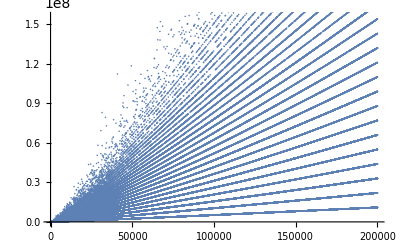

```mathematica
aa=Table[Prime[n+1]^2-Prime[n]^2,{n,2,200000}];ListPlot[aa]
```

下图是前20000个点的图像

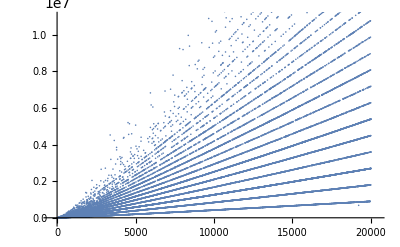

对20000点和200000点图像最下方的曲线斜率估计如下

```mathematica
9.2*10^6/200000//N
```

46.

```mathematica
866730/20000//N
```

43.3365

而且这将可能蕴含着孪生素数的出现分布和n是伪线性相关的

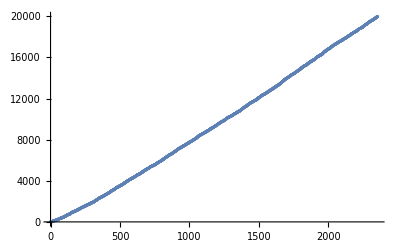

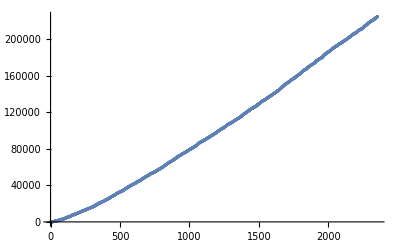

```mathematica
d=4;
aaa=Select[Range[2,20000],Prime[#]-Prime[#-1]==d&];f=Fit[aaa,{1,x},x];
ListPlot[aaa]
ListPlot[Prime[aaa]]
```

发现这些曲线并不会因为整体变粗(振幅误差增大)而导致直线相互合并
所以，初步断言，这些曲线的分立与相邻两素数差的分立性有关
于是作下图

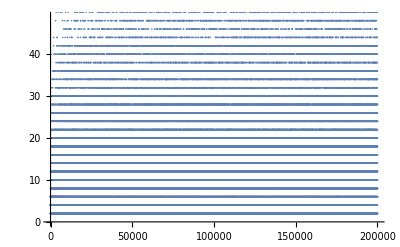

```mathematica
aa=Table[Prime[n+1]-Prime[n],{n,2,200000}];ListPlot[aa]
```

图中的现象是可以预见的，但是当n足够大的时候，这一分立性是否存在还有待考察，正如证明孪生素数无穷多一样，如果差为2k的素数对有无穷多，那么对应的我们可以猜测其稠密性也将成立

而这一稠密性将可以直接证明相邻两个素数的平方差的序列为一簇分立的直线
这是因为(P_(i+1))^2-P_i^2=(P_(i+1)+P_i)(P_(i+1)-P_i)，于是P_(i+1)-P_i的分立性将诱导对应平方差的分立性

由此我们可以推断出，任意次方差都将有分立性，但是将不一定是分立的直线，而是抛物线，三次曲线等等。

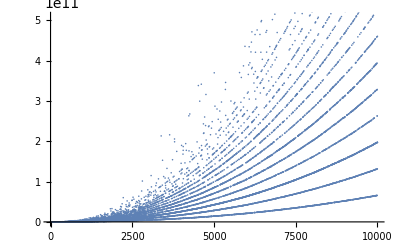

```mathematica
aa=Table[Prime[n+1]^3-Prime[n]^3,{n,2,10000}];ListPlot[aa]
```

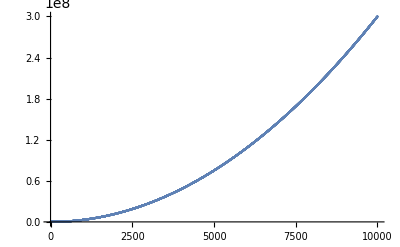

```mathematica
bb=Table[(n+1)^3-n^3,{n,2,10000}];ListPlot[bb]
```

```mathematica
aa=Table[Prime[n+1]^4-Prime[n]^4,{n,2,10000}];ListPlot[aa]
```

-Graphics-

注：对应的三阶的9个相邻素数组成的行列式，相对而言就没有那么好观察到的性质了，这主要与行列式的复杂性有关，这里就不再多做讨论。

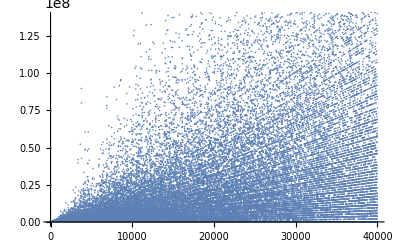

```mathematica
n=2;a=Table[Abs[Det[Table[Prime[i (n+1)+j+l],{i,0,n},{j,0,n}]]],{l,3,40000}];ListPlot[a]
```